```mathematica
g=9.8; (*grav. constant*)
l=0.5; (*length of pendulum*)

θ0=20*π/180; (*20 degrees*)
ω0 = 0; (*starting from rest*)
(*ϕ=y;
t=x;*)
ode1={θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0};
sol=NDSolve[ode1,θ,{t,0,20}];
```

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

```mathematica
myplot1 = Plot[(180/Pi) θ[t]/.sol,{t,0,20},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
omega=√(g/l);
```

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
approx = (180/Pi) θ0 Cos[omega*t];
myplot2=Plot[approx,{t,0,20},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];
```

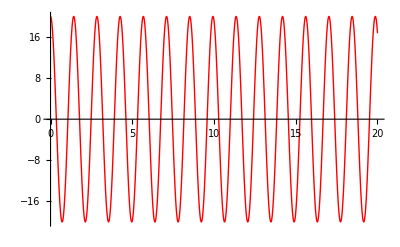

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
th = 50*π/180;
vt = 100;
ode2 = {x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==30*Cos[ 50*π/180],y[0]== 2,y'[0]== 30*Sin[ 50*π/180]}
```

{x''[t]==-0.00098 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+(y'[t] √(x'[t]^2+y'[t]^2))/10000),x[0]==0,x'[0]==30 Sin[(2 π)/9],y[0]==2,y'[0]==30 Cos[(2 π)/9]}

```mathematica
sol = NDSolve[ode2,{x,y},{t,0,200}]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

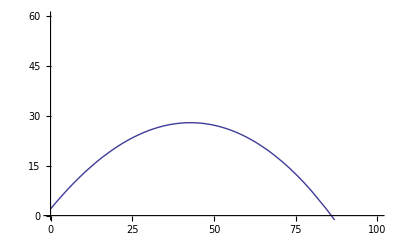

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,100},PlotRange->{{0,100},{0,60}}]
```

```mathematica
g = 9.8 (*m/s^2*);
v =30;
vt=100;
θ=50 π/180;
ode2 = {x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==30*Cos[ 50*π/180],y[0]== 2,y'[0]== 30*Sin[ 50*π/180]};
sol = NDSolve[ode2,{x,y},{t,0,200}];
Manipulate [
ParametricPlot[
Evaluate[
{x[t],y[t], v Cos[θ]t,z+v  Sin[θ]t-4.9t^2}/.
NDSolve[{x''[t]==(-g x'[t]/ vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t]==-g(1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]), x[0]==0,y[0]==z, x'[0]== v*Cos[θ], y'[0]==v*Sin[θ]}, {x,y},{t,0,200}]],
 {t, 0, tf}, PlotRange->{{0,100},{-10,50}},AxesLabel->{"range (m)","height (m)"},ImageSize->1000],
{{tf,0.01,"time(s)"},0.01,10, Appearance->"Labeled"}, 
{{v,10,"Initial Velocity(m/s)"},0.01,100, Appearance->"Labeled"},
{{g,9.8,"Gravity(m/s^s"}, 0.01,4*9.8, Appearance->"Labeled"},
{{vt, 60, "Terminal Velocity(m/s)"}, 1.0, 200, Appearance->"Labeled"},
{{z,2, "Starting Height(m)"}, 0.0, 5, Appearance->"Labeled"},
{{θ,50 Pi/180,"θ(rad/s)"},0.01,π , Appearance->"Labeled"}]
```

```mathematica
Table[expr,{BaseBall,{θ=5π/18,Vinit=34}},{GolfBall,{θ=0.6,Vinit=34}},{HumanCannonball,{θ=1.29,Vinit=46}}]
```

{{{expr,expr},{expr,expr}},{{expr,expr},{expr,expr}}}

```mathematica
(* Sorry, I left for home Friday afternoon and spent Thursday studying for a Linear Midterm. I ended up getting home at 11:10pm, and did not have enough time. It's on me, but I just wanted to let you know if you read this. *)
```